```mathematica
F[r_]:=Factorial[r]/(2^(r/2)*Factorial[r/2])
```

```mathematica
Table[{r,F[r]},{r,2,10,2}]
```

{{2,1},{4,3},{6,15},{8,105},{10,945}}

```mathematica
coeff[n_,k_]:=Binomial[2n,n-k-1]*Binomial[n+k-1,k]/(n)
```

```mathematica
order = 10
```

10

```mathematica
G[x_]:=2/(1+x)
```

```mathematica
TableForm[Table[Table[coeff[n,k],{k,0,n-1}],{n,1,8}]]
```

1 |  |  |  |  |  |  | 
2 | 1 |  |  |  |  |  | 
5 | 6 | 2 |  |  |  |  | 
14 | 28 | 20 | 5 |  |  |  | 
42 | 120 | 135 | 70 | 14 |  |  | 
132 | 495 | 770 | 616 | 252 | 42 |  | 
429 | 2002 | 4004 | 4368 | 2730 | 924 | 132 | 
1430 | 8008 | 19656 | 27300 | 23100 | 11880 | 3432 | 429

```mathematica
alist=MonomialList[Sum[Sum[coeff[n,k]*(-1)^k*f^(n+k),{k,0,n}]*G[x]^n,{n,1,order}],f]
```

{-(4978688 f^19)/(1+x)^10,(49786880 f^18)/(1+x)^10,f^17 (-222576640/(1+x)^10+732160/(1+x)^9),f^16 (584263680/(1+x)^10-6589440/(1+x)^9),f^15 (-993248256/(1+x)^10+26138112/(1+x)^9-109824/(1+x)^8),f^14 (1135140864/(1+x)^10-59744256/(1+x)^9+878592/(1+x)^8),f^13 (-873185280/(1+x)^10+86169600/(1+x)^9-3041280/(1+x)^8+16896/(1+x)^7),f^12 (436592640/(1+x)^10-80424960/(1+x)^9+5913600/(1+x)^8-118272/(1+x)^7),f^11 (-128993280/(1+x)^10+47523840/(1+x)^9-6988800/(1+x)^8+349440/(1+x)^7-2688/(1+x)^6),f^10 (17199104/(1+x)^10-16293888/(1+x)^9+5031936/(1+x)^8-559104/(1+x)^7+16128/(1+x)^6),f^9 (2489344/(1+x)^9-2050048/(1+x)^8+512512/(1+x)^7-39424/(1+x)^6+448/(1+x)^5),f^8 (366080/(1+x)^8-256256/(1+x)^7+49280/(1+x)^6-2240/(1+x)^5),f^7 (54912/(1+x)^7-31680/(1+x)^6+4320/(1+x)^5-80/(1+x)^4),f^6 (8448/(1+x)^6-3840/(1+x)^5+320/(1+x)^4),f^5 (1344/(1+x)^5-448/(1+x)^4+16/(1+x)^3),f^4 (224/(1+x)^4-48/(1+x)^3),f^3 (40/(1+x)^3-4/(1+x)^2),(8 f^2)/(1+x)^2,(2 f)/(1+x)}

```mathematica
Table[Apart[alist[[Length[alist]-i+1]]/f^i],{i,1,order}]
```

{2/(1+x),8/(1+x)^2,40/(1+x)^3-4/(1+x)^2,224/(1+x)^4-48/(1+x)^3,1344/(1+x)^5-448/(1+x)^4+16/(1+x)^3,8448/(1+x)^6-3840/(1+x)^5+320/(1+x)^4,54912/(1+x)^7-31680/(1+x)^6+4320/(1+x)^5-80/(1+x)^4,366080/(1+x)^8-256256/(1+x)^7+49280/(1+x)^6-2240/(1+x)^5,2489344/(1+x)^9-2050048/(1+x)^8+512512/(1+x)^7-39424/(1+x)^6+448/(1+x)^5,17199104/(1+x)^10-16293888/(1+x)^9+5031936/(1+x)^8-559104/(1+x)^7+16128/(1+x)^6}

```mathematica
TableForm[Table[Sum[(-1)^k*coeff[n,k]*f^(n+k),{k,0,n-1}],{n,1,15}]]
```

f
2 f^2-f^3
5 f^3-6 f^4+2 f^5
14 f^4-28 f^5+20 f^6-5 f^7
42 f^5-120 f^6+135 f^7-70 f^8+14 f^9
132 f^6-495 f^7+770 f^8-616 f^9+252 f^10-42 f^11
429 f^7-2002 f^8+4004 f^9-4368 f^10+2730 f^11-924 f^12+132 f^13
1430 f^8-8008 f^9+19656 f^10-27300 f^11+23100 f^12-11880 f^13+3432 f^14-429 f^15
4862 f^9-31824 f^10+92820 f^11-157080 f^12+168300 f^13-116688 f^14+51051 f^15-12870 f^16+1430 f^17
16796 f^10-125970 f^11+426360 f^12-852720 f^13+1108536 f^14-969969 f^15+570570 f^16-217360 f^17+48620 f^18-4862 f^19
58786 f^11-497420 f^12+1918620 f^13-4434144 f^14+6789783 f^15-7189182 f^16+5325320 f^17-2722720 f^18+918918 f^19-184756 f^20+16796 f^21
208012 f^12-1961256 f^13+8498776 f^14-22309287 f^15+39369330 f^16-48992944 f^17+43835792 f^18-28180152 f^19+12748164 f^20-3863080 f^21+705432 f^22-58786 f^23
742900 f^13-7726160 f^14+37182145 f^15-109359250 f^16+218718500 f^17-313112800 f^18+328768440 f^19-254963280 f^20+144865500 f^21-58786000 f^22+16166150 f^23-2704156 f^24+208012 f^25
2674440 f^14-30421755 f^15+161056350 f^16-524924400 f^17+1174173000 f^18-1902160260 f^19+2294669520 f^20-2086063200 f^21+1428499800 f^22-727476750 f^23+267711444 f^24-67395888 f^25+10400600 f^26-742900 f^27
9694845 f^15-119759850 f^16+691945800 f^17-2476437600 f^18+6129183060 f^19-11090902680 f^20+15123958200 f^21-15781521600 f^22+12658095450 f^23-7763631876 f^24+3583214712 f^25-1206469600 f^26+280073300 f^27-40116600 f^28+2674440 f^29

```mathematica
Sum[(-1)^(k)*(G[x])^(2m+1-k)*coeff[2m+1-k,k]/(4(2m+1-k)(2m+1-k-1/2)),{k,0,m}]
```

2^(-1+2 m) (1/(1+x))^(1+2 m) [m]

```mathematica
Table[HypergeometricPFQ[{1/2-m,1-m,-2 m},{1-2 m,3/2-2 m},(1+x)/2],{m,1,10}]
```

{1,1-(2 (1+x))/5,1-(2 (1+x))/3+5/56 (1+x)^2,1-(12 (1+x))/13+35/143 (1+x)^2+7/429 (-1-x) (1+x)^2,1-(20 (1+x))/17+63/136 (1+x)^2-15/221 (1+x)^3+(105 (1+x)^4)/38896,1-(10 (1+x))/7+99/133 (1+x)^2-55/323 (1+x)^3+(165 (1+x)^4)/10336-(99 (1+x)^5)/235144,1-(42 (1+x))/25+1001/920 (1+x)^2-39/115 (1+x)^3+(9009 (1+x)^4)/174800-(1001 (1+x)^5)/297160+(3003 (1+x)^6)/47545600,1-(56 (1+x))/29+130/87 (1+x)^2-154/261 (1+x)^3+(1001 (1+x)^4)/8004-(91 (1+x)^5)/6670+(1001 (1+x)^6)/1520760-(143 (1+x)^7)/15511752,1-(24 (1+x))/11+(5355 (1+x)^2)/2728-(9282 (1+x)^3)/9889+(5525 (1+x)^4)/21576-(357 (1+x)^5)/8990+(10829 (1+x)^6)/3308320-(221 (1+x)^7)/1819576+(663 (1+x)^8)/502864640,1-(90 (1+x))/37+646/259 (1+x)^2-570/407 (1+x)^3+(188955 (1+x)^4)/403744-(12597 (1+x)^5)/133052+(20995 (1+x)^6)/1862728-(969 (1+x)^7)/1330520+(4199 (1+x)^8)/195852544-(4199 (1+x)^9)/22620968832}

```mathematica
Sum[(-1)^(k)*(G[x])^(2m-k)*coeff[2m-k,k]/(4(2m-k)(2m-k-1/2)),{k,0,m}]
```

(2^(-3+2 m) (1+x)^(-2 m) Binomial[4 m,-1+2 m] HypergeometricPFQ[{1/2-m,1-m,-2 m},{1-2 m,3/2-2 m},(1+x)/2])/(m^2 (-1+4 m))

```mathematica
Table[HypergeometricPFQ[{1/2-m,1-m,-2 m},{1-2 m,3/2-2 m},2/(1+2)],{m,1,10}]
```

{1,7/15,17/63,1919/11583,6731/65637,16825/264537,593971/15043725,103993619/4240525203,720057773/47255525955,164704959361/17392520684385}

```mathematica
FindSequenceFunction[{1,7/15,17/63,1919/11583,6731/65637,16825/264537,593971/15043725,103993619/4240525203},x]
```

FindSequenceFunction[{1,7/15,17/63,1919/11583,6731/65637,16825/264537,593971/15043725,103993619/4240525203},x]

```mathematica
F[m_,x_]:=(G[x])^(m)*1/(m(m+1))-Sum[(-1)^(k)*G[x]^(m-k)*coeff[m-k,k]/(4(m-k)(m-k-1/2)),{k,0,Floor[m/2]}]
```

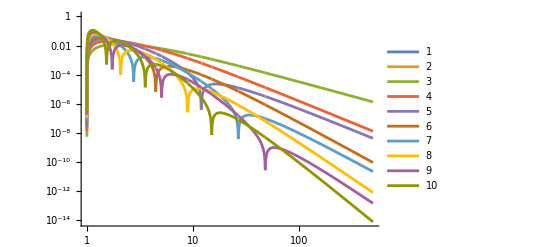

```mathematica
LogLogPlot[Evaluate[Table[Abs[F[n,x]],{n,1,10}]],{x,1,500}, PlotLegends->Automatic]
```

```mathematica
Sum[(-1)^k*Gamma[x] / Gamma[x+4m-2k]*1/(4(2m-k)(2m-k-1/2)),{k,0,m}]
```

∑_(k=0)^m ((-1)^k Gamma[x])/(4 (-1/2-k+2 m) (-k+2 m) Gamma[-2 k+4 m+x])

```mathematica
FullSimplify[Sum[f^n*G[x]^n/(n(n+1)),{n,1,∞}]]
```

1+((1-2 f+x) Log[1-(2 f)/(1+x)])/(2 f)

```mathematica
Integrate[x*Exp[-x^2/2], {x,0,1},Assumptions->x∈Reals]
```

1-1/(√ⅇ)

```mathematica
-NIntegrate[x*y*z*Exp[-(x^2+y^2+z^2)/2]*x^2/(x^2+y^2+z^2)*Log[x^2/(x^2+y^2+z^2)],{x,0,∞}, {y,0,∞},{z,0,∞},WorkingPrecision->10]-NIntegrate[1/Pi^3 * Exp[-x^2-y^2-a^2-b^2-c^2-d^2]*(1+2*(x*y+a*b)/(x^2+y^2+a^2+b^2+c^2+d^2))*Log[1+2*(x*y+a*b)/(x^2+y^2+a^2+b^2+c^2+d^2)], {x,-∞,∞},{y,-∞,∞},{a,-∞,∞},{b,-∞,∞},{c,-∞,∞},{d,-∞,∞}, WorkingPrecision->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.09087851122 and 0.000581015403 for the integral and error estimates.

0.186899717

```mathematica
Rationalize[0.18689971657320970484461932444560727683`9.704986465617816,10^-6]
```

214/1145

```mathematica
-2*NIntegrate[x*y*Exp[-(x^2+y^2)/2]*x^2/(x^2+y^2)*Log[x^2/(x^2+y^2)],{x,0,∞}, {y,0,∞}]
```

0.5

```mathematica
-NIntegrate[x*y*z*Exp[-(x^2+y^2+z^2)/2]*x^2/(x^2+y^2+z^2)*Log[x^2/(x^2+y^2+z^2)],{x,0,∞}, {y,0,∞},{z,0,∞},WorkingPrecision->16]
```

0.2777777776057834

```mathematica
-4*NIntegrate[x*y*z*t*Exp[-(x^2+y^2+z^2+t^2)/2]*x^2/(x^2+y^2+z^2+t^2)*Log[x^2/(x^2+y^2+z^2+t^2)],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},WorkingPrecision->15]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.270833335428663 and 1.0176633969514×10^-6 for the integral and error estimates.

1.08333334171465

```mathematica
-5*NIntegrate[FullSimplify[x*y*z*t*w*Exp[-(x^2+y^2+z^2+t^2+w^2)/2]*x^2/(x^2+y^2+z^2+t^2+w^2)*Log[x^2/(x^2+y^2+z^2+t^2+w^2)]],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},{w,0,∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.25666731922277668618 and 0.000013037813116167567386 for the integral and error estimates.

1.2833365961138834309

```mathematica
-NIntegrate[FullSimplify[x*y*z*t*w*Exp[-(x^2+y^2+z^2+t^2+w^2)/2]*(x^2)/(x^2+y^2+z^2+t^2+w^2)*Log[(x^2)/(x^2+y^2+z^2+t^2+w^2)]],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},{w,0,∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.25666731922277668618 and 0.000013037813116167567386 for the integral and error estimates.

0.25666731922277668618

```mathematica
-NIntegrate[FullSimplify[x*y*z*t*w*Exp[-(x^2+y^2+z^2+t^2+w^2)/2]*(x^2+y^2)/(x^2+y^2+z^2+t^2+w^2)*Log[(x^2+y^2)/(x^2+y^2+z^2+t^2+w^2)]],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},{w,0,∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.31333343855359936198 and 0.000020568029257935534962 for the integral and error estimates.

0.31333343855359936198

```mathematica
-NIntegrate[FullSimplify[x*y*z*t*w*Exp[-(x^2+y^2+z^2+t^2+w^2)/2]*(x^2+y^2+z^2)/(x^2+y^2+z^2+t^2+w^2)*Log[(x^2+y^2+z^2)/(x^2+y^2+z^2+t^2+w^2)]],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},{w,0,∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.27000003697027177065 and 0.000014787936562812687123 for the integral and error estimates.

0.27000003697027177065

```mathematica
-NIntegrate[FullSimplify[x*y*z*t*w*Exp[-(x^2+y^2+z^2+t^2+w^2)/2]*(x^2+y^2+z^2+t^2)/(x^2+y^2+z^2+t^2+w^2)*Log[(x^2+y^2+z^2+t^2)/(x^2+y^2+z^2+t^2+w^2)]],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},{w,0,∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.16000083866797140165 and 0.000010725529490965252467 for the integral and error estimates.

0.16000083866797140165

```mathematica
FindGeneratingFunction[{1/4,5/18,26/144,154/600,1044/4320},x]
```

FindGeneratingFunction[{1/4,5/18,13/72,77/300,29/120},x]

```mathematica
Rationalize[0.2566673192227766861819622403610262323`20.+0.0,10^-5]
```

77/300

```mathematica
Rationalize[0.31333343855359936198`20.+0.0,10^-5]
```

47/150

```mathematica
Rationalize[0.16000083866797140165+0.0,10^-5]
```

4/25

```mathematica
-NIntegrate[FullSimplify[x*y*z*t*w*u*v*Exp[-(x^2+y^2+z^2+t^2+w^2+u^2+v^2)/2]*x^2/(x^2+y^2+z^2+t^2+w^2+u^2+v^2)*Log[x^2/(x^2+y^2+z^2+t^2+w^2+u^2+v^2)]],{x,10^(-4),∞}, {y,10^(-4),∞},{z,10^(-4),∞},{t,10^(-4),∞},{w,10^(-4),∞}, {u,10^(-4),∞}, {v,10^(-4),∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.22757141405903968488 and 0.00069341757566486985772 for the integral and error estimates.

0.22757141405903968488

```mathematica
Rationalize[0.22757141405903968488*7,10^-4]
```

137/86

```mathematica
N[15/18,10]
```

0.8333333333

```mathematica
Integrate[x*Exp[-x^2/2]*a^4/(x^2+b+a^2)^2,{x,0,∞},Assumptions->a∈Reals,Assumptions->b∈Reals]
```

ConditionalExpression[a^4 (1/(2 (a^2+b))+1/4 ⅇ^(1/2 (a^2+b)) (CoshIntegral[1/2 (-a^2-b)]-Log[-a^2-b]+Log[a^2+b]-SinhIntegral[1/2 (a^2+b)])), ]

```mathematica
Simplify[a^2 (1/(2 (a^2+b))+1/4 ⅇ^(1/2 (a^2+b)) (CoshIntegral[1/2 (-a^2-b)]-Log[-a^2-b]+Log[a^2+b]-SinhIntegral[1/2 (a^2+b)]))]
```

a^2 (1/(2 (a^2+b))+1/4 ⅇ^(1/2 (a^2+b)) (CoshIntegral[1/2 (-a^2-b)]-Log[-a^2-b]+Log[a^2+b]-SinhIntegral[1/2 (a^2+b)]))

```mathematica
NIntegrate[(x*y*z*t)*Exp[-(x^2+y^2+z^2+t^2)/2]*(x*y*z*t)^2/(x^2+y^2+z^2+t^2)^4,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞}, WorkingPrecision->12]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.00119047607441

```mathematica
Integrate[x^(2k-2m)*Exp[-t*x/2],{x,0,∞},Assumptions->k-m>0]
```

ConditionalExpression[2^(1+2 k-2 m) t^(-1-2 k+2 m) Gamma[1+2 k-2 m], Re[t]>0]

```mathematica
{Integrate[1/x^(2*2+3),x,x,x,x]*5!,Integrate[1/x^(2*3+3),x,x,x,x,x,x]*7!,Integrate[1/x^(2*4+3),x,x,x,x,x,x,x,x]*9!,Integrate[1/x^(2*5+3),x,x,x,x,x,x,x,x,x,x]*11!}
```

{1/(3 x^3),1/(4 x^3),1/(5 x^3),1/(6 x^3)}

```mathematica
Integrate[(x^2+y^2+z^2)^nExp[-t/2(x+y+z)],{x,0,∞},{y,0,∞},{z,0,∞}]
```

∫_0^∞ ∫_0^∞ ∫_0^∞ (x^2+y^2+z^2)^nExp[-1/2 t (x+y+z)]ⅆzⅆyⅆx

```mathematica
Factor[16k(k-1)(k-2)(k-3)+6*4*24k(k-1)(k-2)+(3*24*24+4*720*2)k(k-1)+40320k]
```

16 k (2118+371 k+30 k^2+k^3)

```mathematica
F2[n_]:=Sum[Binomial[n,k]/Binomial[2n,2k],{k,0,n}]/( (2n+1))
```

```mathematica
F3[n_]:=Sum[Binomial[n,k]/Binomial[2n,2k]*(2k+1)/(2n+1)F2[k],{k,0,n}]/( (n+1))
```

```mathematica
F[n_]:=Sum[Binomial[n,k]/Binomial[2n,2k]*(Hypergeometric2F1[1/2,1,1/2-k,-1]/(1+2 k)+Hypergeometric2F1[1,3/2+k,3/2,-1]),{k,0,n}]/( (n+1)(2n+1))
```

```mathematica
Table[F3[m],{m,1,10}]
```

{1/2,4/15,16/105,7/75,47/770,4448/105105,463/15015,1195/51051,26997/1469650,263324/17782765}

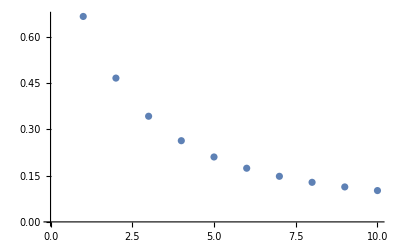

```mathematica
ListPlot[Table[Hypergeometric2F1[1/2,1,1/2-x,-1]/(1+2 x)+Hypergeometric2F1[1,3/2+x,3/2,-1],{x,1,10}]]
```

```mathematica
DSolve[y''''''''[x]==16 k (2118+371 k+30 k^2+k^3)/x^(k+8),y[x],x]
```

{{y[x]→(16 (2118+371 k+30 k^2+k^3) x^-k)/((1+k) (2+k) (3+k) (4+k) (5+k) (6+k) (7+k))+C[1]+x C[2]+x^2 C[3]+x^3 C[4]+x^4 C[5]+x^5 C[6]+x^6 C[7]+x^7 C[8]}}

```mathematica
FullSimplify[Sum[1/(2n(2n-1)),{n,1,∞}]]/Log[2]
```

1

```mathematica
Apart[-(f (3+f+3 x))/(3 (1+x)^2)]
```

-f^2/(3 (1+x)^2)-f/(1+x)

```mathematica
Ap[x_,y_,z_]:=1/2+1/2*Sqrt[1-4*x^2*z^2/(x^2+y^2+z^2)^2]
```

```mathematica
Am[x_,y_,z_]:=1/2-1/2*Sqrt[1-4*x^2*z^2/(x^2+y^2+z^2)^2]
```

```mathematica
-NIntegrate[x*y*z*Exp[-(x^2+y^2+z^2)/2]*(Ap[x,y,z]*Log[Ap[x,y,z]]+Am[x,y,z]*Log[Am[x,y,z]]),{x,0,∞}, {y,0,∞},{z,0,∞},WorkingPrecision->20,Exclusions->{0,0,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.2850220624915902623620493720206354628109800928226296192713581029455553 and 1.403416516981714857961508438111766594570930462415143586330282027283369×10^-6 for the integral and error estimates.

0.28502206249159026236

```mathematica
n:=1
```

```mathematica
Table[{n,NIntegrate[Exp[-(x+y)/2]*((x^2+y^2)/(x+y)^(2))^n,{x,0,∞}, {y,0,∞},WorkingPrecision->20],NIntegrate[Exp[-(x+y+z)/2]*((x^2+y^2+z^2)/(x+y+z)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞},WorkingPrecision->20],NIntegrate[Exp[-(x+y+z+t)/2]*((x^2+y^2+z^2+t^2)/(x+y+z+t)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞},{t,0,∞},WorkingPrecision->20],
NIntegrate[Exp[-(x+y+z+t+u)/2]*((x^2+y^2+z^2+t^2+u^2)/(x+y+z+t+u)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞},{t,0,∞},{u,0,∞},WorkingPrecision->20],
NIntegrate[Exp[-(x+y+z+t+u+v)/2]*((x^2+y^2+z^2+t^2+u^2+v^2)/(x+y+z+t+u+v)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞},{t,0,∞},{u,0,∞},{v,0,∞},WorkingPrecision->20],
NIntegrate[Exp[-(x+y+z+t+u+v+w)/2]*((x^2+y^2+z^2+t^2+u^2+v^2+w^2)/(x+y+z+t+u+v+w)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞},{t,0,∞},{u,0,∞},{v,0,∞},{w,0,∞},WorkingPrecision->20]},{n,3,4}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.219047548665992859753991674848027984533880104577116109741972664731837 and 8.767300949485567640471469934579385677334428744175404860572050935798539×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.269841268478868761347381954688927204255135121784274607346452254153879 and 1.162729467206231199987320220460836597958758309664778565393988964590943×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.4730156406849635676 and 0.000028934121756013213933 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{3,1.3714285714283338342,1.2190475486659928598,1.2698412684788687613,1.4730156406849635676,1.8469888584624693433,2.4561107652192130279},{4,1.0539682539679593739,0.74666666665831978274,0.63815296776088230701,0.6218369762354118513,0.66777715533713582308,0.7731675446834398633}}

```mathematica
Table[NIntegrate[Exp[-(x+y)/2]*((x^2+y^2)/(x+y)^(2))^n,{x,0,∞}, {y,0,∞},WorkingPrecision->20]/4,{n,1,10}]
```

{0.66666666666665009778,0.46666666666666005113,0.34285714285708345855,0.26349206349198984346,0.2106782106782992571,0.17415917415924282495,0.14794094794103526974,0.12844279903107668549,0.11347290480422095936,0.10165376419247920756}

```mathematica
Rationalize[{1,0.66666666666665009777519961830525387424`20.,0.46666666666666005112663072308784701234`20.,0.34285714285708345854711756460900507248`20.,0.26349206349198984346490357650651575978`20.,0.21067821067829925709618651438349706092`20.,0.1741591741592428249539118596018017176`20.,0.14794094794103526973923817057869736538`20.,0.12844279903107668549441888441097408253`20.,0.11347290480422095935903112145100551969`20.,0.10165376419247920755760776199399010131`20.},10^(-12)]
```

{1,2/3,7/15,12/35,83/315,146/693,523/3003,952/6435,14051/109395,26206/230945,32867/323323}

```mathematica
FunctionExpand[FindSequenceFunction[{1,2/3,7/15,12/35,83/315,146/693,523/3003,952/6435},x],Assumptions->Element[x,Reals]]
```

-(ⅈ 2^-x √π Gamma[x])/Gamma[1/2+x]-Hypergeometric2F1[1,1/2+x,1+x,2]/x

```mathematica
Table[F[x],{x,1,5}]
```

{2/3,7/15,12/35,83/315,146/693}

```mathematica
Table[NIntegrate[Exp[-(x+y+z)/2]*((x^2+y^2+z^2)/(x+y+z)^(2))^n,{x,0,∞}, {y,0,∞},{z,0,∞},WorkingPrecision->20]/8,{n,1,6}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.000000000049695815817360423280011041258109977340062806929570233891903 and 2.574291390919929669310153774427417645005421708954266283855232818851105×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.133333333286986433831998199949278781290267186030123075366723055073779 and 1.168606302094142440059254317864116741657898380477747100851744340063918×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.219047548665992859753991674848027984533880104577116109741972664731837 and 8.767300949485567640471469934579385677334428744175404860572050935798539×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{0.50000000000621197698,0.26666666666087330423,0.15238094358324910747,0.093333333332289972842,0.061038961040018923973,0.04231958517594003707}

```mathematica
Rationalize[{0.50000000000621197697717005291000138016`20.,0.26666666666087330422899977499365984766`20.,0.15238094358324910746924895935600349807`20.,0.09333333333228997284203573109354227077`20.,0.06103896104001892397340758019825099414`20.,0.0423195851759400370698413159256500558`20.},10^(-5)]
```

{1/2,4/15,16/105,7/75,13/213,8/189}

```mathematica
FindSequenceFunction[{1,1/2,4/15,16/105,7/75,13/213,8/189},x]
```

FindSequenceFunction[{1,1/2,4/15,16/105,7/75,13/213,8/189},x]

4/87

```mathematica
Table[{n,NIntegrate[x*y*Exp[-(x^2+y^2)/2]*((x^4)/(x^2+y^2)^(2))^n,{x,0,∞}, {y,0,∞},WorkingPrecision->20],NIntegrate[x*y*z*Exp[-(x^2+y^2+z^2)/2]*((x^4)/(x^2+y^2+z^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞},WorkingPrecision->20],NIntegrate[x*y*z*t*Exp[-(x^2+y^2+z^2+t^2)/2]*((x^4)/(x^2+y^2+z^2+t^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞},WorkingPrecision->20],NIntegrate[x*y*z*t*u*Exp[-(x^2+y^2+z^2+t^2+u^2)/2]*((x^4)/(x^2+y^2+z^2+t^2+u^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞}, {u,0,∞},WorkingPrecision->20],NIntegrate[x*y*z*t*u*v*Exp[-(x^2+y^2+z^2+t^2+u^2+v^2)/2]*((x^4)/(x^2+y^2+z^2+t^2+u^2+v^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞}, {u,0,∞}, {v,0,∞},WorkingPrecision->20],NIntegrate[x*y*z*t*u*v*w*Exp[-(x^2+y^2+z^2+t^2+u^2+v^2+w^2)/2]*((x^4)/(x^2+y^2+z^2+t^2+u^2+v^2+w^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞}, {u,0,∞}, {v,0,∞}, {w,0,∞},WorkingPrecision->20]},{n,2,4}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.066666666055160363536 and 1.1487422971016100848×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.028571429691979055337 and 6.4518367010550848641×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0142857167583558 and 8.62729480083682×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

$Aborted

```mathematica
arrn2:=Rationalize[{1,1.37142857142833383418847025843602028994`20.,1.21904754866599285975399167484802798453`20.,1.26984126847886876134738195468892720426`20.,1.47301564068496356755574031686749054511`20.,1.84698885846246934328534082113372786168`20.,2.45611076521921302792244458064604014426`20.},10^(-6)]
```

```mathematica
arrn3:=Rationalize[{2,1.05396825396795937385961430602606303911`20.,0.7466666666583197827362858487483381662`20.,0.63815296776088230701314808072145547706`20.,0.6218369762354118512960477596393803205`20.,0.66777715533713582307925735849395982358`20.,0.77316754468343986330054148112792551769`20.},10^(-7)]
```

```mathematica
arrn3
```

{1,332/315,56/75,746/1169,467/751,601/900,559/723}

```mathematica
Table[arrn3[[x]]/2^x,{x,1,7}]
```

{1,83/315,7/75,843/21136,1327/68288,1403/134464,2115/350144}

```mathematica
Table[(16 (2118+371 k+30 k^2+k^3))/((1+k) (2+k) (3+k) (4+k) (5+k) (6+k) (7+k)),{k,1,7}]
```

{1,83/315,7/75,691/17325,202/10395,94/9009,272/45045}

1+(2 (x^2+x y+y^2))/(x+y+z)^2-(2 (x+y))/(x+y+z)

```mathematica
arrn3
```

{1,12/35,16/105,5/63,4/87,3/104,1/52}

```mathematica
Apart[(5+x)/((1+x)(2+x)(3+x))]
```

2/(1+x)-3/(2+x)+1/(3+x)

```mathematica
Table[2/(1+x)-3/(2+x)+4/(3+x)-5/(4+x)+6/(5+x)+1/(6+x),{x,1,7}]
```

{8/7,727/840,899/1260,103/168,3743/6930,2683/5544,3767/8580}

```mathematica
FindSequenceFunction[{1,2/3,7/15,12/35,83/315,146/693,523/3003},n]
```

-(2^(1-n) (ⅈ √π n!+2^n (1/2 (-1+2 n))! Hypergeometric2F1[1,1/2+n,1+n,2]) Pochhammer[1,-1+n])/(√π n! Pochhammer[3/2,-1+n])

```mathematica
Table[NIntegrate[x*y*z*Exp[-(x^2+y^2+z^2)/2]*((x^4+y^4+z^4)/(x^2+y^2+z^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞},PrecisionGoal->20],{n,0,8}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.16501×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.5 and 1.28825×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.266667 and 1.09516×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{1.,0.5,0.266667,0.152381,0.0933333,0.061039,0.0423196,0.0308358,0.023408}

```mathematica
Rationalize[{1.0000000000105012,0.5000000000101862,0.26666666667996014,0.15238095242468214,0.09333333379521588,0.06103896107029914,0.042319585170905866,0.030835830816556904,0.02340796457646466},10^(-5)]
```

{1,1/2,4/15,16/105,7/75,13/213,8/189,7/227,7/299}

```mathematica
RSolve[f[x]-(x-1)/(x-1+2n)*f[x-1]==0,f[x],x]
```

{{f[x]→(C[1] Pochhammer[1,-1+x])/Pochhammer[1+2 n,-1+x]}}

```mathematica
Simplify[(C[1] Pochhammer[1,-1+x])/Pochhammer[1+2 n,-1+x]]
```

(C[1] Pochhammer[1,-1+x])/Pochhammer[1+2 n,-1+x]

```mathematica
FunctionExpand[(C[1] Pochhammer[1,-1+x])/Pochhammer[1+2 n,-1+x]]
```

(C[1] Gamma[1+2 n] Gamma[x])/Gamma[2 n+x]

```mathematica
y-y*Sum[(Gamma[1+2 n] Gamma[x]*y^n)/(x^(2n-1)Gamma[2 n+x]*n*(n+1)),{n,1,∞}]/Log[2]
```

y-(y^2 Gamma[x] HypergeometricPFQ[{1,1,3/2,2},{3,1+x/2,3/2+x/2},y/x^2])/(x Gamma[2+x] Log[2])

```mathematica
FullSimplify[y-(y^2 Gamma[x] HypergeometricPFQ[{1,1,3/2,2},{3,1+x/2,3/2+x/2},y/x^2])/(x Gamma[2+x] Log[2])]
```

y-(y^2 HypergeometricPFQ[{1,1,3/2,2},{3,1+x/2,3/2+x/2},y/x^2])/(x^2 (1+x) Log[2])

```mathematica
F[x_,f_]:=2*f-2*(f^2 HypergeometricPFQ[{1,1,3/2,2},{3,1+x/2,3/2+x/2},f/x^2])/(x^2 (1+x) Log[2])
```

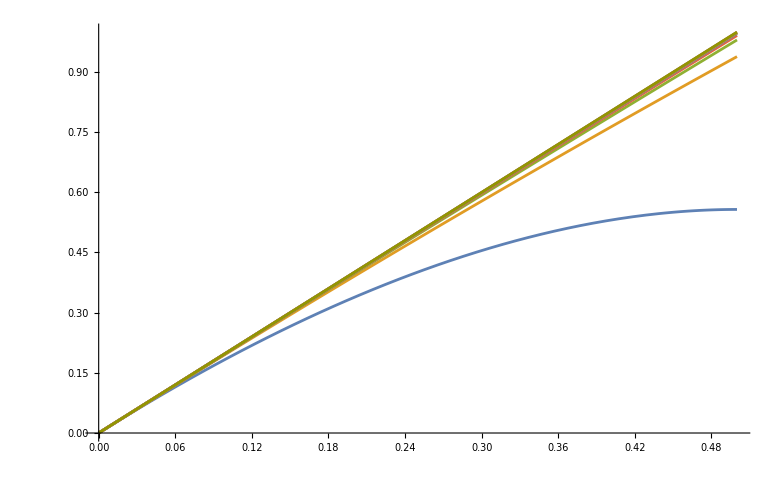

```mathematica
Plot[Evaluate[Table[F[n,x],{n,1,10}]],{x,0,0.5}]
```

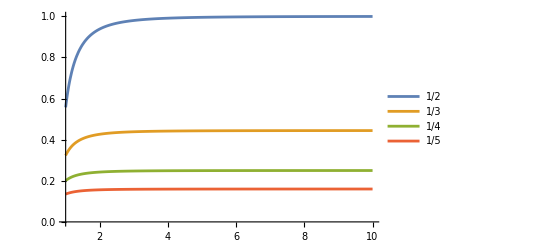

Power::infy: Infinite expression 1/0 encountered.

Integrate::idiv: Integral of -1/2 Log[(1-2 x^2+√(1-4 Power[«2»]))/(2 x)] does not converge on {0,∞}.

```mathematica
Plot[Evaluate[Table[2/n*F[x, 1/n],{n,2,5}]],{x,1,10},PlotLegends->{f=1/2,f=1/3,f=1/4,f=1/5}]
```

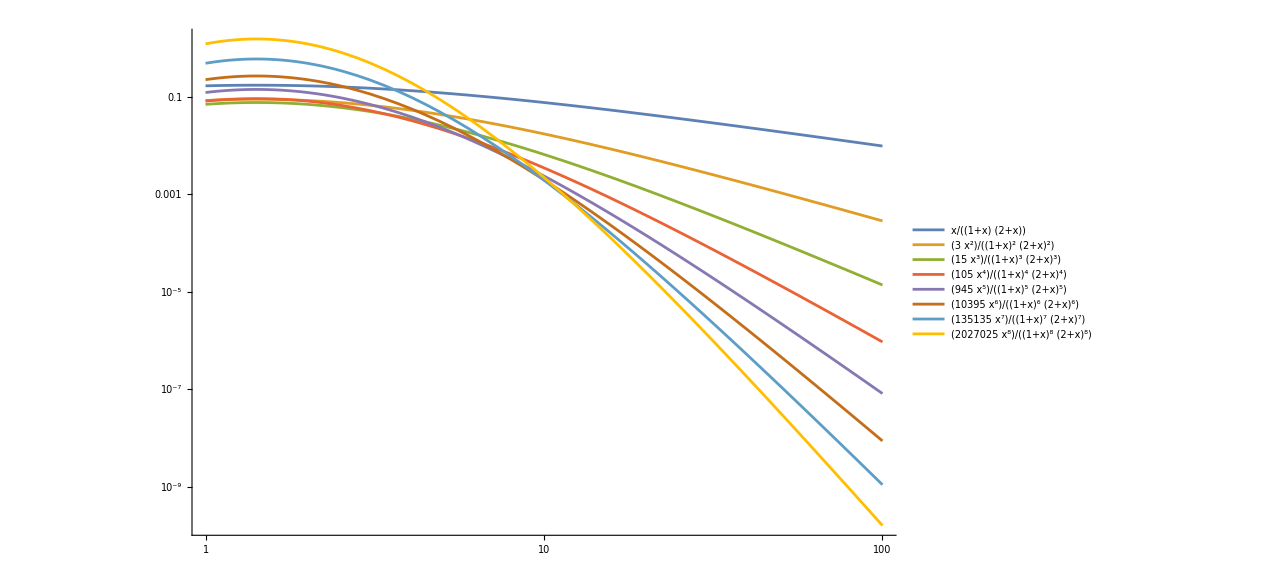

```mathematica
LogLogPlot[Evaluate[Table[(2r)!/(2^r*r!)*x^r/((1+x)^r(2+x)^r),{r,1,8}]],{x,1,100}, PlotLegends->"Expressions"]
```

```mathematica
Factor[Sum[(l-1)^2,{l,2,La+1}]+Sum[(2*La-l+1)^2,{l,La+2,2*La}]]
```

1/3 La (1+2 La^2)

```mathematica
Table[Sum[KroneckerDelta[i1+i6,i5+i7]*KroneckerDelta[i2+i4,i1+i3]*KroneckerDelta[i5+i3,i2+i4]*KroneckerDelta[i6,i7],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La}],{La,1,10}]
```

{1,12,57,176,425,876,1617,2752,4401,6700}

```mathematica
FindGeneratingFunction[{1,10,45,136,325,666,1225,2080,3321,5050,7381,10440,14365,19306,25425},x]
```

(-1-5 x-5 x^2-x^3)/(-1+x)^5

```mathematica
Table[Sum[KroneckerDelta[i1+i7,i2+i8]*KroneckerDelta[i2+i3,i1+i6]*KroneckerDelta[i4+i8,i3+i5]*KroneckerDelta[i5+i6,i4+i7],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La}],{La,1,8}]
```

{1,16,103,408,1209,2960,6335,12272}

```mathematica
Chi[q1_,q2_,La_]:=1/L*Sum[Exp[i*2*Pi*(q1-q2)/L*i],{i,1,La}]
```

```mathematica
Table[Sum[KroneckerDelta[i1+i4,i3+i6]*KroneckerDelta[i1,i2]*KroneckerDelta[i3+i6,i2+i5]*KroneckerDelta[i4,i5],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La}],{La,2,10}]
```

{6,19,44,85,146,231,344,489,670}

```mathematica
Table[Sum[KroneckerDelta[i1,i2]*KroneckerDelta[i2+i3,i1+i4]*KroneckerDelta[i4+i5,i3+i6]*KroneckerDelta[i6+i7,i5+i8]*KroneckerDelta[i8+i9,i7+i10]*KroneckerDelta[i9,i10],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La},{i9,1,La},{i10,1,La}],{La,2,5}]
```

{32,243,1024,3125}

```mathematica
Table[Sum[KroneckerDelta[i1,i2]*KroneckerDelta[i2+i3,i1+i4]*KroneckerDelta[i4+i5,i3+i6]*KroneckerDelta[i6+i7,i5+i8]*KroneckerDelta[i8+i9,i7+i10]*KroneckerDelta[i10+i11,i9+i12]*KroneckerDelta[i12+i13,i11+i14]*KroneckerDelta[i13,i14],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La},{i9,1,La},{i10,1,La},{i11,1,La},{i12,1,La},{i13,1,La},{i14,1,La}],{La,2,2}]
```

{128}

```mathematica
Factor[La^4+2*Sum[i^4,{i,1,La-1}]]
```

1/15 La (-1+10 La^2+6 La^4)

```mathematica
Decompose[La^3/L^3+2/L^3*HarmonicNumber[-1+La,-3],f=La/L]
```

{La^2/(2 L^3)+La^4/(2 L^3)}

```mathematica
|
```

```mathematica
FullSimplify[Sum[Exp[I*2*Pi*q/L*l],{l,1,La}]-Sum[Exp[-I*2*Pi*q/L*l],{l,1,La}]]
```

2 ⅈ Csc[(π q)/L] Sin[(La π q)/L] Sin[((1+La) π q)/L]

```mathematica
Table[Sum[KroneckerDelta[i1+i5,i2+i8]*KroneckerDelta[i2+i7,i1+i6]*KroneckerDelta[i3+i4,i5+i7]*KroneckerDelta[i3+i4,i6+i8],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La}],{La,1,8}]
```

{1,16,103,408,1209,2960,6335,12272}

```mathematica
T[l_,La_]:=Piecewise[{{l-1,l<=La+1},{2La+1-l,l>La+1}}]
```

```mathematica
Table[Sum[KroneckerDelta[i1-i2,i7-i8]*KroneckerDelta[i1-i2,i3-i4]*KroneckerDelta[i1-i2,i5-i6],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La}],{La,1,8}]
```

{1,18,115,452,1333,3254,6951,13448}

```mathematica
Table[Sum[KroneckerDelta[i1-i2,i7-i8]*KroneckerDelta[i5-i6,i3-i4]*KroneckerDelta[i1-i2,i5-i6],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La}],{La,1,6}]
```

{1,18,115,452,1333,3254}

```mathematica
Table[Sum[T[i2+i6,La]*T[i4+i6,La],{i2,1,La},{i4,1,La},{i6,1,La}],{La,1,20}]
```

{1,18,121,488,1459,3590,7707,14960,26877,45418,73029,112696,167999,243166,343127,473568,640985,852738,1117105,1443336}

```mathematica
Simplify[Sum[KroneckerDelta[i,j+x],{i,1,La},{j,1,La}],Assumptions->{Element[La,Integers],Element[x,Integers],Abs[x]<La}]
```

Piecewise[{{1, (La==1+x&&x≥0)||(La+x==1&&x<0)}, {La-x, La>1+x&&x≥0}, {La+x, x<0&&La+x>1}, {0, True}}]

```mathematica
II[La_,f_]:=2/3*La*f^2+1/(3L)*f
```

```mathematica
Decompose[14*La*f^4+
28*f^2*II[La,f]+
5*(2/5*La*f^4+2/(3*L)*f^3-1/(15*L^3)*f)+
32*f*(1/2*La*f^3+1/(2L)*f^2)+
22*(11/30La*f^4+1/(2L)*f^3+2/(15L^3)*f)+
4*(9/20La*f^4+5/(12L)*f^3+2/(15L^3)*f)
,f]
```

{(47 La)/(15 L^4)+(124 La^3)/(3 L^4)+(908 La^5)/(15 L^4)}

```mathematica
g[x_]:=2/(1+x)
```

```mathematica
Sp[f_,x_]:=1-(f*g[x]/2+2/9f^2*g[x]^2+11/30*f^3*g[x]^3+908/(15*8*7)*f^4*(-(f (4 f^2+5 f (1+x)+15 (1+x)^2))/(15 (1+x)^3)+(√2 √f ArcTanh[(√2 √f)/(√(1+x))])/(√(1+x))+1/2 Log[1-(2 f)/(1+x)]))/Log[2]
```

```mathematica
Sm[f_,x_]:=1-(f*g[x]/2+2/9f^2*g[x]^2+11/30*f^3*g[x]^3+908/(15*8*7)*f^4*g[x]^4)/Log[2]
```

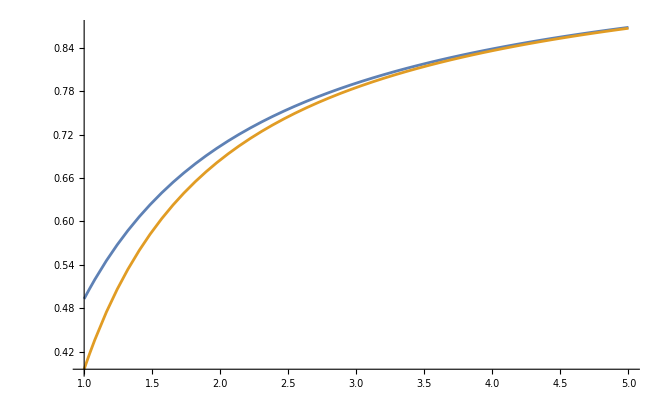

```mathematica
Plot[{Sp[1/2,x],Sm[1/2,x]},{x,1,5}]
```

```mathematica
N[{Sm[1/2,3],Sp[1/2,3]},10]
```

{0.7852685116,0.7913521713}

```mathematica
FullSimplify[Sum[f^n*g[1]^n/(2n(2n-1)),{n,1,∞}]]
```

√f ArcTanh[√f]+1/2 Log[1-f]